## Rosenzweig-MacArthur consumer-resource model with parasitism and a directly transmitted parasite

### Parasites increase host mortality rate in a resource-independent way

The full model assumes logistic growth of the resource (R), with a Type II functional response for both susceptible (S) and infected (Q and Q_m) hosts. We assume that all hosts are born susceptible, and that the birth rates for susceptible and infected hosts are identical. There are two strains of pathogen circulating in the population, the resident and mutant. These strains differ in their virulence (v and v_m, respectively) and transmission rates; we assume that transmission rate is a function of virulence according to β(v)=β_0 v/(1+v). 

To determine whether the mutant can invade, we need to evaluate the stability of the mutant-free equilibrium, which can do by looking at the eigenvalues of the Jacobian matrix. Notice that the Jacobian is block upper triangular, so the eigenvalues are given by the eigenvalues of the block-diagonal matrix

```mathematica
(* The model *)
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q + Qm);
dS=(es fs R)/(h+R) (S+Q + Qm)-d S-β[v] S Q -β[vm] S Qm;
dQ=β[v] S Q-(d+v) Q;
dQm=β[vm] S Qm-(d+vm) Qm;

(* Stability analysis *)
(* Calculate the Jacobian *)
J=Simplify[{{D[dR,R],D[dR,S],D[dR,Q], D[dR,Qm]},{D[dS,R],D[dS,S],D[dS,Q], D[dS,Qm]},
{D[dQ,R],D[dQ,S],D[dQ,Q], D[dR,Qm]},
{D[dQm,R],D[dQm,S],D[dQm,Q], D[dQm,Qm]}}]
(* Evaluate the Jacobian at the equilibrium of interest (Qm=0) *)
MatrixForm[J/.{Qm->0}]
```

{{(-fs h K (Q+Qm+S)+(K-2 R) (h+R)^2 ρ)/(K (h+R)^2),-(fs R)/(h+R),-(fs R)/(h+R),-(fs R)/(h+R)},{(es fs h (Q+Qm+S))/(h+R)^2,-d+(es fs R)/(h+R)-Q β[v]-Qm β[vm],(es fs R)/(h+R)-S β[v],(es fs R)/(h+R)-S β[vm]},{0,Q β[v],-d-v+S β[v],-(fs R)/(h+R)},{0,Qm β[vm],0,-d-vm+S β[vm]}}

((-fs h K (Q+S)+(K-2 R) (h+R)^2 ρ)/(K (h+R)^2) | -(fs R)/(h+R) | -(fs R)/(h+R) | -(fs R)/(h+R)
(es fs h (Q+S))/(h+R)^2 | -d+(es fs R)/(h+R)-Q β[v] | (es fs R)/(h+R)-S β[v] | (es fs R)/(h+R)-S β[vm]
0 | Q β[v] | -d-v+S β[v] | -(fs R)/(h+R)
0 | 0 | 0 | -d-vm+S β[vm])

If the system goes to a stable equilibrium, the invasion fitness of the mutant is given by r=β(v_m)Ŝ-(v_m+d), where Ŝ is the equilibrium abundance of susceptibles, set by the resident.

```mathematica
r=-d-vm+S β[vm];
```

#### Finding the singular strategy when the resident dynamics go to a stable equilibrium

If the resident dynamics approach the stable equilibrium, we should be able to calculate the singular strategy analytically. This will be a useful comparison point for situations where the dynamics are not stable. From the fact that, at equilibrium, dQ/dt=0, we can immediately calculate that Ŝ=((1+v)(d+v))/(β_0 v).

```mathematica
(* Calculating the equilibrium *)
Solve[dQ==0,S]
r=r/.Solve[dQ==0,S][[1]]
```

{{S→(d+v)/β[v]}}

-d-vm+((d+v) β[vm])/β[v]

```mathematica
Simplify[D[r,vm]/.{vm->v}]
```

-1+((d+v) β'[v])/β[v]

The singular strategy is given by the value of v that satisfies (d+v)β'(v)-β(v)=0.

We can also assess whether any such singular strategy will be evolutionarily stable by looking at the second derivative. You can see that this depends on the sign of β''(v): if β''(v)<0 (that is, if transmission rate is a saturating function of virulence), then the singular strategy will be evolutionarily stable.

```mathematica
Simplify[D[r,{vm,2}]/.{vm->v}]
```

((d+v) β''[v])/β[v]

We can assess whether the singular strategy is convergence stable by looking at the derivative of the fitness gradient with respect to the resident trait. Note that the numerator (which is sign-determining) can be written as β(v)(d+v)β''(v)-β'(v)((d+v)β'(v)-β(v)). At the singular strategy, we have that (d+v)β'(v)-β(v)=0, so the convergence stability condition is just β(v)(d+v)β''(v)<0, which is identical to the evolutionarily stability condition. Thus, a saturating relationship between virulence and transmission guarantees that any singular strategy will be both convergence stable and evolutionarily stable.

```mathematica
Simplify[D[D[r,vm]/.{vm->v},v]]
Numerator[Simplify[D[D[r,vm]/.{vm->v},v]]]==-β'[v] ((d+v) β'[v]-β[v])+β[v] (d+v) β''[v]//Simplify
```

(-(d+v) β'[v]^2+β[v] (β'[v]+(d+v) β''[v]))/β[v]^2

True

If we specify a functional form for β(v), we can go even further, and actually calculate the singular strategy.

For example, if we assume that β(v)=(β_0 v)/(1+v), then the singular strategy is given by ((d + v) β_0)/(1+v)^2-(β_0 v)/(1+v)=β_0/(1+v)^2(d-v^2)=0. From this, you can see that the singular value of v is v=√d.

Thus, if the dynamics go to an equilibrium, there is one singular strategy that is both evolutionarily and convergence stable. You can also see that there is no dependence of the singular strategy or the fitness gradient on host resources, indicating that changes in resources will have no effect when the system is stable. It seems plausible that resources will have no effect when the dynamics are unstable, though that remains to be seen. If that is the case, then you might expect the ESS to be fairly similar in both stable and unstable populations, so whether the parasite will stabilize the host dynamics or not depends on how close the resident-only system is to the stability boundary. If the system is just barely unstable in the absence of any parasitism, then the addition of parasites will tend to stabilize.

#### Calculating the invasion exponent

In general, whether a mutant can invade or not depends on the traits (parameters) of the resident. This dependence is “felt” through the effect of the resident on the dynamics of the system. 

From the above calculations, we know that whether the mutant parasite “strain” can invade or not depends on the abundance of susceptible hosts, which is determined by the traits of the resident parasite strain. To determine whether the mutant can invade, then, we need to determine the dynamics of the susceptible host population. 

If the susceptible host population goes to an equilibrium, then we can simply plug this equilibrium into the invasion exponent expression. If the host population cycles, on the other hand, then we need to calculate the average host abundance over the cycle, 1/T(∫_0)^T S(t) dt. 

For now, the only two parameters we are interested in varying are the resource carrying capacity (K) and the virulence of the resident parasite (v), so we write a new function, ‘CalcAvgS,’ that takes those two parameters as arguments, along with a parameter ‘dt’ that determines how accurate our Riemann sum approximation of the integral will be. 

First, let’s confirm that we can get different dynamics by varying the resource carrying capacity.

With K=1, the system approaches a stable equilibrium:

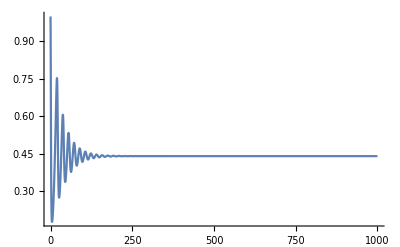

```mathematica
params={K->1,v->1,ρ->1,fs->1,h->1,d->0.1,v->0.1,B0->5,es->0.5};
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v) Q;
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},AccuracyGoal->Infinity, PrecisionGoal->10];
Plot[S[t]/.soln, {t, 0, 1000},PlotRange->All]
```

With K=2, the system cycles:

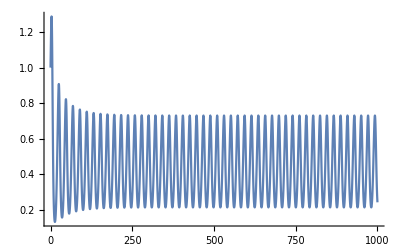

```mathematica
params={K->2,ρ->1,fs->1,h->1,d->0.1,v->0.1,B0->5,es->0.5};
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v) Q;
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},AccuracyGoal->Infinity, PrecisionGoal->10];
Plot[S[t]/.soln, {t, 0, 1000},PlotRange->All]
```

The boundary between stability and cycles when K = 2 can be found by playing around with values of d and v.

```mathematica
(* Fitness gradient *)
```

#### Using the secant method to find the singular strategies

```mathematica
fitGrad[{thisK_,thisv_,thisB0_,dt_}]:=Module[{params,K,v,ρ,fs,h,d,B0,es,dR,R,S,Q,dS,dQ,Eq,EndEq,AvgS,soln,St,FirstPeak,T,SecondPeak,Ssum},
params={K->thisK,v->thisv,ρ->1,fs->1,h->1,d->0.1,B0->thisB0,es->0.5};
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v) Q;

(* Calculate the equilibria of the system *)
Eq=Solve[{dR==0,dS==0,dQ==0},{R,S,Q}]/.params;
(* Which equilibrium represents the endemic equilibrium with all values positive? *)
EndEq=Eq⟦Position[Table[AllTrue[Eq⟦i,;;,2⟧,#>0&],{i,1,Length[Eq]}],True]⟦1,1⟧⟧;
(* Does the Jacobian evaluated at this equilibrium have all negative eigenvalues e.g. is the equilibrium stable? *)
AvgS=If[AllTrue[Re[Eigenvalues[{{D[dR,R],D[dR,S],D[dR,Q]},{D[dS,R],D[dS,S],D[dS,Q]},{D[dQ,R],D[dQ,S],D[dQ,Q]}}/.params/.EndEq]],#<0&],
(* if all e-values are negative, return the equilibrium S *)
EndEq⟦2,2⟧,
(* otherwise, numerically solve *)
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},AccuracyGoal->Infinity, PrecisionGoal->10];
St=Table[(S[t]/.soln)⟦1⟧,{t,800,900,dt}];
(* find the first peak of the cycle *)	
FirstPeak= 800+Position[St,Max[St]]⟦1,1⟧ dt;
(* Find next peak *)
St=Table[(S[t]/.soln)⟦1⟧,{t,FirstPeak,1000,dt}];
(* Cycle period *)
T=Position[Table[(St⟦t⟧-St⟦t+1⟧)/(St⟦t+1⟧-St⟦t+2⟧),{t,1,Length[St]-2}],_?(#<0&)]⟦2,1⟧ dt;
(* Next peak *)
SecondPeak=FirstPeak+T;
(* Riemann sum to find the integral of S(t) over the cycle *)
Ssum=Sum[dt (S[t]/.soln)⟦1⟧,{t,FirstPeak+dt/2,SecondPeak+dt/2,dt}];
(* calculate the average S *)
Ssum/T
];
(B0 AvgS-(1+v)^2)/(1+v)^2/.params
];
```

A better way to do it will be to write a custom root finding algorithm. We can do this using the secant method, which is essentially a finite difference approximation of Newton’s method, since we cannot compute the derivative of the fitness gradient with respect to v. To use this method, you must provide two initial values for v, and then you converge from there using the recursion relation v_n=(v_(n-2)f(v_(n-1))-v_(n-1)f(v_(n-2)))/(f(v_(n-1))-f(v_(n-2))).

```mathematica
calcvBounds[{Kval_,B0val_}]:=Module[{ρ,K,fs,h,es,d,B0,v,params,bounds},
params={K->Kval,ρ->1,fs->1,h->1,d->0.1,B0->B0val,es->0.5};
(* Figure out when the per-capita growth rate of the infectious class is equal to zero, when the susceptible population is at its maximum *)
bounds=Solve[(B0 v)/(1+v)((es h (-d h-d K+es fs K) ρ)/((d-es fs)^2 K))-d-v==0,v]/.params;
{Min[bounds[[;;,1,2]]],Max[bounds[[;;,1,2]]]}
]
```

```mathematica
secantMethod[{v0init_,v1init_,Kval_,B0val_,convcrit_}]:=Module[{v0uncon,v1uncon,v0con,v1con,conv,g0,g1,v2con,v2uncon,vbnds},
(* set the unconstrained v values for use in calculating the fitness gradient *)
v0uncon=v0init;
v1uncon=v1init;
(* calculate the bounds on v *)
vbnds=calcvBounds[{Kval,B0val}];
(* convert v to the unconstrained scale for use in the recurrence relation *)
v0con=Log[((v0uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v0uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
v1con=Log[((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
(* Set the initial value of the convergence measure *)
conv=1;
While[conv>convcrit,
(* compute the value of the fitness gradient at the unconstrained values of v0 and v1 *)
g0=fitGrad[{Kval,v0uncon,B0val,0.001}];
g1=fitGrad[{Kval,v1uncon,B0val,0.001}];
(* use the recurrence relation to update the constrained value of v *)
v2con=(v0con g1-v1con g0)/(g1-g0);
(* compute the unconstrained version *)
v2uncon=Exp[v2con]/(1+Exp[v2con]) (Max[vbnds]-Min[vbnds])+Min[vbnds];
v2uncon=If[v2uncon==Min[vbnds],Min[vbnds]+0.0001,v2uncon];
v2uncon=If[v2uncon==Max[vbnds],Max[vbnds]-0.0001,v2uncon];
(* set the convergence criterion to the lower of g1 and g2 *)
conv=Min[{Abs[g0],Abs[g1]}];
(* update the unconstrained and constrained values of v0 and v1 *)
v0uncon=v1uncon;
v0con=v1con;
v1uncon=v2uncon;
v1con=Log[((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
];
v2uncon
]
```

The value I would expect is v=√d=√0.1=0.316228.

```mathematica
Sqrt[0.1]
```

This is exactly what I see for K=1, which produces a stable equilibrium at the initial parameter values.

```mathematica
secantMethod[{0.1,0.11,1,5,10^-12}]
```

0.316228

But it is also what I get when K=2, which produces a stable limit cycle at the initial parameter values.

```mathematica
secantMethod[{0.1,0.11,2,5,10^-12}]
```

0.316228

Thus, if no aspect of virulence, transmission, or host background mortality depends on resources, resources will have no effect on the evolution of virulence.

Below you can see that the reason the singular strategies are the same for the equilibrium and cycling cases is because the average S over the cycle is equal to the S value at the equilibrium.

```mathematica
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v) Q;
params={K->4,ρ->1,fs->1,h->1,d->0.01,v->0.1,B0->10,es->0.5};
dt=0.001;
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},AccuracyGoal->Infinity, PrecisionGoal->10];
(*Print[Plot[S[t]/.soln,{t,800,1000}]];*)
(* Find the average S over the cycle *)
St=Table[(S[t]/.soln)⟦1⟧,{t,800,900,dt}];
(* find the first peak of the cycle *)	
FirstPeak= 800+Position[St,Max[St]]⟦1,1⟧ dt;
(* Find next peak *)
St=Table[(S[t]/.soln)⟦1⟧,{t,FirstPeak,1000,dt}];
(* Cycle period *)
T=Position[Table[(St⟦t⟧-St⟦t+1⟧)/(St⟦t+1⟧-St⟦t+2⟧),{t,1,Length[St]-2}],_?(#<0&)]⟦2,1⟧ dt;
(* Next peak *)
SecondPeak=FirstPeak+T;
(* Riemann sum to find the integral of S(t) over the cycle *)
Ssum=Sum[dt (S[t]/.soln)⟦1⟧,{t,FirstPeak+dt/2,SecondPeak+dt/2,dt}];
(* print the average S over the cycle *)
AvgS=Ssum/T
```

0.120998

```mathematica
(* At equilibrium: *)
params={K->2,ρ->1,fs->1,h->1,d->0.01,v->0.1,B0->10,es->0.5};
Eq=Solve[{dR==0,dS==0,dQ==0}/.params,{R,S,Q}];
EndEq=Eq⟦Position[Table[AllTrue[Table[{AllTrue[Re[Eq⟦i,;;,2⟧],#>0&],AllTrue[Im[Eq⟦i,;;,2⟧],#<10^-9&]},{i,1,Length[Eq]}][[j]],#==True&],{j,1,Length[Eq]}],True]⟦1,1⟧⟧
```

{R→0.246661,S→0.121,Q→0.97191}

### Parasites increase host mortality rate in a resource-independent way, second function

```mathematica
r=-d-vm+S β[vm];
```

#### Finding the singular strategy when the resident dynamics go to a stable equilibrium

If the resident dynamics approach the stable equilibrium, we should be able to calculate the singular strategy analytically. This will be a useful comparison point for situations where the dynamics are not stable. From the fact that, at equilibrium, dQ/dt=0, we can immediately calculate that Ŝ=((1+v)(d+v))/(β_0 v).

```mathematica
(* Calculating the equilibrium *)
Solve[dQ==0,S]
r=r/.Solve[dQ==0,S][[1]]
```

{{S→(d+v)/β[v]}}

-d-vm+((d+v) β[vm])/β[v]

```mathematica
Simplify[D[r,vm]/.{vm->v}]
```

-1+((d+v) β'[v])/β[v]

The singular strategy is given by the value of v that satisfies (d+v)β'(v)-β(v)=0.

We can also assess whether any such singular strategy will be evolutionarily stable by looking at the second derivative. You can see that this depends on the sign of β''(v): if β''(v)<0 (that is, if transmission rate is a saturating function of virulence), then the singular strategy will be evolutionarily stable.

```mathematica
Simplify[D[r,{vm,2}]/.{vm->v}]
```

((d+v) β''[v])/β[v]

We can assess whether the singular strategy is convergence stable by looking at the derivative of the fitness gradient with respect to the resident trait. Note that the numerator (which is sign-determining) can be written as β(v)(d+v)β''(v)-β'(v)((d+v)β'(v)-β(v)). At the singular strategy, we have that (d+v)β'(v)-β(v)=0, so the convergence stability condition is just β(v)(d+v)β''(v)<0, which is identical to the evolutionarily stability condition. Thus, a saturating relationship between virulence and transmission guarantees that any singular strategy will be both convergence stable and evolutionarily stable.

```mathematica
Simplify[D[D[r,vm]/.{vm->v},v]]
Numerator[Simplify[D[D[r,vm]/.{vm->v},v]]]==-β'[v] ((d+v) β'[v]-β[v])+β[v] (d+v) β''[v]//Simplify
```

(-(d+v) β'[v]^2+β[v] (β'[v]+(d+v) β''[v]))/β[v]^2

True

If we specify a functional form for β(v), we can go even further, and actually calculate the singular strategy.

For example, if we assume that β(v)=β_0+(β_1 v)/(1+v) (so that the parasite can transmit, even if virulence is 0), then the singular strategy is given by

```mathematica
Solve[(D[-d-vm+((d+v) β[vm])/β[v]/.{β[vm]->β0+(β1 vm)/(1+vm),β[v]->β0+(β1 v)/(1+v)},vm]/.{vm->v})==0,v]
```

{{v→(-β0-√(-β0 β1+d β0 β1+d β1^2))/(β0+β1)},{v→(-β0+√(-β0 β1+d β0 β1+d β1^2))/(β0+β1)}}

```mathematica
Simplify[(D[-d-vm+S β[vm]/.{β[vm]->β0+(β1 vm)/(1+vm)},vm]/.{vm->v})]
```

-(1+2 v+v^2-S β1)/(1+v)^2

#### Using the secant method to find the singular strategies

```mathematica
fitGrad[{thisK_,thisv_,thisB0_,thisB1_,dt_}]:=Module[{params,K,v,ρ,fs,h,d,B0,B1,es,dR,R,S,Q,dS,dQ,Eq,EndEq,AvgS,soln,St,FirstPeak,T,SecondPeak,Ssum},
params={K->thisK,v->thisv,ρ->1,fs->1,h->1,d->0.1,B0->thisB0,B1->thisB1,es->0.5};
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d S-(B0+(B1 v)/(1+v)) S Q;
dQ=(B0+(B1 v)/(1+v)) S Q-(d+v) Q;

(* Calculate the equilibria of the system *)
Eq=Solve[{dR==0,dS==0,dQ==0},{R,S,Q}]/.params;
(* Which equilibrium represents the endemic equilibrium with all values positive? *)
EndEq=Eq⟦Position[Table[AllTrue[Eq⟦i,;;,2⟧,#>0&],{i,1,Length[Eq]}],True]⟦1,1⟧⟧;
(* Does the Jacobian evaluated at this equilibrium have all negative eigenvalues e.g. is the equilibrium stable? *)
AvgS=If[AllTrue[Re[Eigenvalues[{{D[dR,R],D[dR,S],D[dR,Q]},{D[dS,R],D[dS,S],D[dS,Q]},{D[dQ,R],D[dQ,S],D[dQ,Q]}}/.params/.EndEq]],#<0&],
(* if all e-values are negative, return the equilibrium S *)
EndEq⟦2,2⟧,
(* otherwise, numerically solve *)
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},AccuracyGoal->Infinity, PrecisionGoal->10];
St=Table[(S[t]/.soln)⟦1⟧,{t,800,900,dt}];
(* find the first peak of the cycle *)	
FirstPeak= 800+Position[St,Max[St]]⟦1,1⟧ dt;
(* Find next peak *)
St=Table[(S[t]/.soln)⟦1⟧,{t,FirstPeak,1000,dt}];
(* Cycle period *)
T=Position[Table[(St⟦t⟧-St⟦t+1⟧)/(St⟦t+1⟧-St⟦t+2⟧),{t,1,Length[St]-2}],_?(#<0&)]⟦2,1⟧ dt;
(* Next peak *)
SecondPeak=FirstPeak+T;
(* Riemann sum to find the integral of S(t) over the cycle *)
Ssum=Sum[dt (S[t]/.soln)⟦1⟧,{t,FirstPeak+dt/2,SecondPeak+dt/2,dt}];
(* calculate the average S *)
Ssum/T
];
-(1+2 v+v^2-AvgS B1)/(1+v)^2/.params
];
```

A better way to do it will be to write a custom root finding algorithm. We can do this using the secant method, which is essentially a finite difference approximation of Newton’s method, since we cannot compute the derivative of the fitness gradient with respect to v. To use this method, you must provide two initial values for v, and then you converge from there using the recursion relation v_n=(v_(n-2)f(v_(n-1))-v_(n-1)f(v_(n-2)))/(f(v_(n-1))-f(v_(n-2))).

```mathematica
calcvBounds[{Kval_,B0val_,B1val_}]:=Module[{ρ,K,fs,h,es,d,B0,B1,v,params,bounds},
params={K->Kval,ρ->1,fs->1,h->1,d->0.1,B0->B0val,B1->B1val,es->0.5};
(* Figure out when the per-capita growth rate of the infectious class is equal to zero, when the susceptible population is at its maximum *)
bounds=Solve[(B0+(B1 v)/(1+v))((es h (-d h-d K+es fs K) ρ)/((d-es fs)^2 K))-d-v==0,v]/.params;
{Min[bounds[[;;,1,2]]],Max[bounds[[;;,1,2]]]}
]
```

```mathematica
secantMethod[{v0init_,v1init_,Kval_,B0val_,B1val_,convcrit_}]:=Module[{v0uncon,v1uncon,v0con,v1con,conv,g0,g1,v2con,v2uncon,vbnds},
(* set the unconstrained v values for use in calculating the fitness gradient *)
v0uncon=v0init;
v1uncon=v1init;
(* calculate the bounds on v *)
vbnds=calcvBounds[{Kval,B0val,B1val}];
(* convert v to the unconstrained scale for use in the recurrence relation *)
v0con=Log[((v0uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v0uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
v1con=Log[((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
(* Set the initial value of the convergence measure *)
conv=1;
While[conv>convcrit,
(* compute the value of the fitness gradient at the unconstrained values of v0 and v1 *)
g0=fitGrad[{Kval,v0uncon,B0val,B1val,0.001}];
g1=fitGrad[{Kval,v1uncon,B0val,B1val,0.001}];
(* use the recurrence relation to update the constrained value of v *)
v2con=(v0con g1-v1con g0)/(g1-g0);
(* compute the unconstrained version *)
v2uncon=Exp[v2con]/(1+Exp[v2con]) (Max[vbnds]-Min[vbnds])+Min[vbnds];
v2uncon=If[v2uncon==Min[vbnds],Min[vbnds]+0.0001,v2uncon];
v2uncon=If[v2uncon==Max[vbnds],Max[vbnds]-0.0001,v2uncon];
(* set the convergence criterion to the lower of g1 and g2 *)
conv=Min[{Abs[g0],Abs[g1]}];
(* update the unconstrained and constrained values of v0 and v1 *)
v0uncon=v1uncon;
v0con=v1con;
v1uncon=v2uncon;
v1con=Log[((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
];
v2uncon
]
```

The value I would expect if β_0=0 is v=√d=√0.1=0.316228.

```mathematica
Sqrt[0.1]
```

This is exactly what I see for K=1, which produces a stable equilibrium at the initial parameter values.

```mathematica
secantMethod[{0.1,0.11,1,0,5,10^-12}]
```

0.316228

The value I would expect if β_0=0.1 is v=0.261134.

```mathematica
Simplify[-β0 β1+d β0 β1+d β1^2>0]
```

β1 ((-1+d) β0+d β1)>0

```mathematica
v->(-β0+√(-β0 β1+d β0 β1+d β1^2))/(β0+β1)/.{β0->0.1,β1->5,d->0.1}
```

v→0.261134

```mathematica
secantMethod[{0.1,0.11,1,0.1,5,10^-12}]
```

0.261134

But it is also what I get when K=2, which produces a stable limit cycle at the initial parameter values.

```mathematica
secantMethod[{0.1,0.11,2,0.1,5,10^-12}]
```

0.261134

```mathematica
secantMethod[{0.1,0.11,3,0.1,5,10^-12}]
```

0.261134

Thus, if no aspect of virulence, transmission, or host background mortality depends on resources, resources will have no effect on the evolution of virulence.

Below you can see that the reason the singular strategies are the same for the equilibrium and cycling cases is because the average S over the cycle is equal to the S value at the equilibrium.

```mathematica
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v) Q;
params={K->4,ρ->1,fs->1,h->1,d->0.01,v->0.1,B0->10,es->0.5};
dt=0.001;
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},AccuracyGoal->Infinity, PrecisionGoal->10];
(*Print[Plot[S[t]/.soln,{t,800,1000}]];*)
(* Find the average S over the cycle *)
St=Table[(S[t]/.soln)⟦1⟧,{t,800,900,dt}];
(* find the first peak of the cycle *)	
FirstPeak= 800+Position[St,Max[St]]⟦1,1⟧ dt;
(* Find next peak *)
St=Table[(S[t]/.soln)⟦1⟧,{t,FirstPeak,1000,dt}];
(* Cycle period *)
T=Position[Table[(St⟦t⟧-St⟦t+1⟧)/(St⟦t+1⟧-St⟦t+2⟧),{t,1,Length[St]-2}],_?(#<0&)]⟦2,1⟧ dt;
(* Next peak *)
SecondPeak=FirstPeak+T;
(* Riemann sum to find the integral of S(t) over the cycle *)
Ssum=Sum[dt (S[t]/.soln)⟦1⟧,{t,FirstPeak+dt/2,SecondPeak+dt/2,dt}];
(* print the average S over the cycle *)
AvgS=Ssum/T
```

0.120998

```mathematica
(* At equilibrium: *)
params={K->2,ρ->1,fs->1,h->1,d->0.01,v->0.1,B0->10,es->0.5};
Eq=Solve[{dR==0,dS==0,dQ==0}/.params,{R,S,Q}];
EndEq=Eq⟦Position[Table[AllTrue[Table[{AllTrue[Re[Eq⟦i,;;,2⟧],#>0&],AllTrue[Im[Eq⟦i,;;,2⟧],#<10^-9&]},{i,1,Length[Eq]}][[j]],#==True&],{j,1,Length[Eq]}],True]⟦1,1⟧⟧
```

{R→0.246661,S→0.121,Q→0.97191}

If β(v)=β_0+(β_1 v)/(1+v), then the singular strategy is given by ((d + v) β_1)/(1+v)^2-β_0-(β_1 v)/(1+v)=β_0/(1+v)^2(d-v^2)=0

```mathematica
Solve[((d+v) β1)/(1+v)^2-β0-(β1 v)/(1+v)==0,v]
```

{{v→(-β0-√(-β0 β1+d β0 β1+d β1^2))/(β0+β1)},{v→(-β0+√(-β0 β1+d β0 β1+d β1^2))/(β0+β1)}}

### Parasites increase host mortality rate in a resource-dependent way

This model is identical to the one above, except in that mortality is resource-dependent. We include this resource-dependence according to the functional form specified in McCauley et al. 2008, which assumed that the mortality rate was equal to μ/(σ f(R)), where σ is the resource assimilation efficiency and f(R) is the functional response of the host. Thus, when resource ingestion is low, the mortality rate increases. For analytical simplicity, we will assume that σ=1 (which is not the same as assuming that the efficiency of turning ingested resources into new hosts, ϵ_S, is also equal to one. Note that this greatly alters the interpretation of the parameter d. In the previous model, d was the mortality rate, and had units of 1/time. Now, d is a mortality scalar that has units of resource/time^2.

To determine whether the mutant can invade, we need to evaluate the stability of the mutant-free equilibrium, which can do by looking at the eigenvalues of the Jacobian matrix. Notice that the Jacobian is block upper triangular, so the eigenvalues are given by the eigenvalues of the block-diagonal matrix

```mathematica
(* The model *)
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q + Qm);
dS=(es fs R)/(h+R) (S+Q + Qm)-(d S)/((fs R)/(h+R))-((B0 v)/(1+v)) S Q -((B0 vm)/(1+vm)) S Qm;
dQ=((B0 v)/(1+v)) S Q-(d+v)/((fs R)/(h+R)) Q;
dQm=((B0 vm)/(1+vm)) S Qm-(d+vm)/((fs R)/(h+R)) Qm;

(* Stability analysis *)
(* Calculate the Jacobian *)
J=Simplify[{{D[dR,R],D[dR,S],D[dR,Q], D[dR,Qm]},{D[dS,R],D[dS,S],D[dS,Q], D[dS,Qm]},
{D[dQ,R],D[dQ,S],D[dQ,Q], D[dR,Qm]},
{D[dQm,R],D[dQm,S],D[dQm,Q], D[dQm,Qm]}}]
(* Evaluate the Jacobian at the equilibrium of interest (Qm=0) *)
MatrixForm[J/.{Qm->0}]
```

{{(-fs h K (Q+Qm+S)+(K-2 R) (h+R)^2 ρ)/(K (h+R)^2),-(fs R)/(h+R),-(fs R)/(h+R),-(fs R)/(h+R)},{(h (d (h+R)^2 S+es fs^2 R^2 (Q+Qm+S)))/(fs R^2 (h+R)^2),(es fs R)/(h+R)-(d (h+R))/(fs R)-(B0 Q v)/(1+v)-(B0 Qm vm)/(1+vm),(es fs R)/(h+R)-(B0 S v)/(1+v),(es fs R)/(h+R)-(B0 S vm)/(1+vm)},{(h Q (d+v))/(fs R^2),(B0 Q v)/(1+v),(B0 S v)/(1+v)-((h+R) (d+v))/(fs R),-(fs R)/(h+R)},{(h Qm (d+vm))/(fs R^2),(B0 Qm vm)/(1+vm),0,(B0 S vm)/(1+vm)-((h+R) (d+vm))/(fs R)}}

((-fs h K (Q+S)+(K-2 R) (h+R)^2 ρ)/(K (h+R)^2) | -(fs R)/(h+R) | -(fs R)/(h+R) | -(fs R)/(h+R)
(h (d (h+R)^2 S+es fs^2 R^2 (Q+S)))/(fs R^2 (h+R)^2) | (es fs R)/(h+R)-(d (h+R))/(fs R)-(B0 Q v)/(1+v) | (es fs R)/(h+R)-(B0 S v)/(1+v) | (es fs R)/(h+R)-(B0 S vm)/(1+vm)
(h Q (d+v))/(fs R^2) | (B0 Q v)/(1+v) | (B0 S v)/(1+v)-((h+R) (d+v))/(fs R) | -(fs R)/(h+R)
0 | 0 | 0 | (B0 S vm)/(1+vm)-((h+R) (d+vm))/(fs R))

If the system goes to a stable equilibrium, the invasion fitness of the mutant is given by r=(β_0 v_m Ŝ)/(1+v_m)-((v_m+d)(h+R̂))/(f_s R̂), where Ŝ is the equilibrium abundance of susceptibles and R̂ is the equilibrium abundance of resources, as these are determined by the interaction among host, resources, and the resident strain.

```mathematica
r=(B0 S vm)/(1+vm)-((h+R) (d+vm))/(fs R);
```

#### Finding the singular strategy when the resident dynamics go to a stable equilibrium

If the resident dynamics approach the stable equilibrium, we can calculate the singular strategy analytically. This will be a useful comparison point for situations where the dynamics are not stable.

```mathematica
dS
```

-(d (h+R) S)/(fs R)+(es fs R (Q+Qm+S))/(h+R)-(B0 Q S v)/(1+v)-(B0 Qm S vm)/(1+vm)

```mathematica
dR
```

-(fs R (Q+Qm+S))/(h+R)+R (1-R/K) ρ

```mathematica
dQ
```

(B0 Q S v)/(1+v)-(Q (h+R) (d+v))/(fs R)

```mathematica
(* The S equilibrium (in terms of R̂) *)
Seq=Solve[dQ==0,S]
(* The Q equilibrium (in terms of R̂) *)
Qeq=Simplify[Solve[(dS/.Qm->0/.Seq[[1]])==0,Q]]
(* The R equilibrium *)
Solve[(dR/.Qm->0/.Qeq[[1]]/.Seq[[1]])==0,R]
```

{{S→((h+R) (1+v) (d+v))/(B0 fs R v)}}

{{Q→((h+R) (-es fs^2 R^2+d (h+R)^2) (1+v) (d+v))/(B0 fs R v (es fs^2 R^2-d (h+R)^2-(h+R)^2 v))}}

{{R→-(2 d h-d K+es fs^2 K+2 h v-K v)/(4 (d-es fs^2+v))-1/2 √1-1/2 √(((2 d h-d K+es fs^2 K+2 h v-K v)^2)/(2 (d-es fs^2+v)^2)-(d K+9)/(B0 (d-es fs^2+v) ρ)-1-1-1^1/1-(-(1)^3/(d-es 1+v)^3+1/(B0 1^2 ρ)-(8 (1))/(B0 (d-es fs^2+v) ρ))/(4 √(5+1/(3 2^1 (1)))))},2,{R→1}}
 |  |  |  |

You can see that R̂ has no simple analytical expression. However, we can write the invasion fitness, r, in terms of this equilibrium. Plugging in the expression for Ŝ (which depends on R̂), r=((v-v_m)(v v_m-d))/(v (1+v_m))1/(f(R̂))

```mathematica
r/.Seq[[1]]//Simplify
```

((h+R) (v-vm) (-d+v vm))/(fs R v (1+vm))

To find the singular strategy, we need to find the root of (∂r)/(∂v_m)|_(v_m=v) . Note, however, that the value of R̂ depends on v. We can simplify the expression to the following: (∂r)/(∂v_m)|_(v_m=v)=1/(f(R̂))(d-v^2)/(v+v^2). From this, it is clear that (∂r)/(∂v_m)|_(v_m=v)=0 only when v=√d, which, interestingly, is the same as the answer when mortality is independent of resources.

```mathematica
(D[r/.Seq[[1]]/.R->R[v],vm]/.vm->v)//Simplify
```

((d-v^2) (h+R[v]))/(fs v (1+v) R[v])

To determine whether this is an ESS, we need to look at whether the derivative (∂^2 r)/(∂v_m^2)|_(v_m=v)≤ 0. Since (∂^2 r)/(∂v_m^2)|_(v_m=v)=-(2 (d+v) (h+R̂(v)))/(fs v (1+v)^2 R̂(v)), it is clear that this inequality is always satisfied and  v=√d will be an evolutionarily stable strategy.

```mathematica
D[r/.Seq[[1]]/.R->R[v],{vm,2}]/.vm->v//Simplify
```

-(2 (d+v) (h+R[v]))/(fs v (1+v)^2 R[v])

To determine whether this is an CSS, we need to look at whether the derivative d/dv((∂r)/(∂v_m)|_(v_m=v))<0. Since (∂r)/(∂v_m)|_(v_m=v)=1/(f(R̂))(d-v^2)/(v+v^2), d/dv((∂r)/(∂v_m)|_(v_m=v))=(-(f'(R̂)R'(v))/(f(R̂))^2)((d-v^2)/(v+v^2))-1/(f(R̂))((d+2d v+v^2)/(v^2 (1+v)^2)). Since we are interested in the value of this derivative when v is at the ESS, we can set v=√d, which leads the vanishing of the first product, and d/dv((∂r)/(∂v_m)|_(v_m=v))=-1/(f(R̂))((d+2d v+v^2)/(v^2 (1+v)^2)). Thus the singular strategy is also a CSS.

Thus, if the dynamics go to an equilibrium, there is one singular strategy that is both evolutionarily and convergence stable. You can also see that there is no dependence of the singular strategy or the fitness gradient on host resources, indicating that changes in resources will have no effect when the system is stable. It seems plausible that resources will have no effect when the dynamics are unstable, though that remains to be seen. If that is the case, then you might expect the ESS to be fairly similar in both stable and unstable populations, so whether the parasite will stabilize the host dynamics or not depends on how close the resident-only system is to the stability boundary. If the system is just barely unstable in the absence of any parasitism, then the addition of parasites will tend to stabilize.

#### Calculating the invasion exponent

```mathematica
r=(B0 S vm)/(1+vm)-((h+R) (d+vm))/(fs R);
```

In general, whether a mutant can invade or not depends on the traits (parameters) of the resident. This dependence is “felt” through the effect of the resident on the dynamics of the system. 

If the host population cycles, r=(B0 S vm)/(1+vm)-((h+R) (d+vm))/(fs R);then we need to calculate the invasion exponent over the cycle, r=(β_0 v_m)/(1+v_m)(1/T(∫_0)^T S(t) dt)-(d+v_m)/f_S(1/T(∫_0)^T(h+R(t))/(R(t)) dt). 

First, let’s confirm that we can get different dynamics by varying the resource carrying capacity.

With K=2, the system approaches a stable equilibrium:

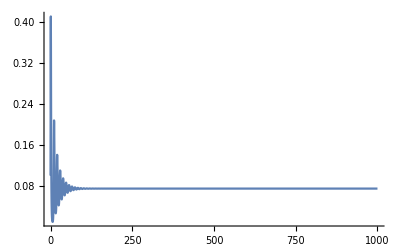

```mathematica
params={K->2,v->1,ρ->1,fs->1,h->1,d->0.01,v->0.1,B0->10,es->0.5};
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-(d S)/((fs R)/(h+R))-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v)/((fs R)/(h+R)) Q;
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},AccuracyGoal->Infinity, PrecisionGoal->10];
Plot[Q[t]/.soln, {t, 0, 1000},PlotRange->All]
```

With K=3, the system cycles:

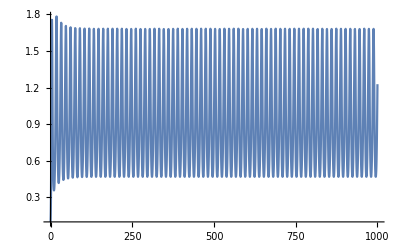

```mathematica
params={K->3,ρ->1,fs->1,h->1,d->0.01,v->0.1,B0->10,es->0.5};
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d/((fs R)/(h+R)) S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v)/((fs R)/(h+R)) Q;
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},AccuracyGoal->Infinity, PrecisionGoal->10];
Plot[Q[t]/.soln, {t, 0, 1000},PlotRange->All]
```

The boundary between stability and cycles when K = 3 can be found by playing around with values of d and v.

#### Using the secant method to find the singular strategies

Here, we need to be more careful about calculating the v bounds. Depending on the value of K and β_0, the v bounds may or may not be positive and real. We need to build in a catch for this possibility in the functions that make use of these bounds.

```mathematica
calcvBounds[{Kval_,B0val_,dval_}]:=Module[{ρ,K,fs,h,es,d,B0,v,params,bounds},
params={K->Kval,ρ->1,fs->1,h->1,d->dval,B0->B0val,es->0.5};
(* Figure out when the per-capita growth rate of the infectious class is equal to zero, when the susceptible population is at its maximum *)
bounds=Solve[((B0 S v)/(1+v)-((h+R) (d+v))/(fs R)/.{R->-(√d h)/(√d-√es fs),S->(√es h (√es fs K-√d (h+K)) ρ)/((√d-√es fs)^2 K)})==0,v]/.params;
{Min[bounds[[;;,1,2]]],Max[bounds[[;;,1,2]]]}
]
```

This function calculate the fitness gradient for a given set of values for K, v, d, and β_0. Note that since the invasion fitness is

```mathematica
fitGrad[{thisK_,thisv_,thisd_,thisB0_,dt_}]:=Module[{params,K,v,ρ,fs,h,d,B0,es,dR,R,S,Q,dS,dQ,Eq,Equil,EndEq,AvgS,soln,St,FirstPeak,T,SecondPeak,Ssum,grad,fsum,Avgf,DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec,DOPRICoefficients},
(* The parameters for the model *)
params={K->thisK,v->thisv,ρ->1,fs->1,h->1,d->thisd,B0->thisB0,es->0.5};
(* Calculate the equilibria of the resident-only model *)
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d/((fs R)/(h+R)) S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v)/((fs R)/(h+R)) Q;
(* Calculate the equilibria of the system, with everything plugged in except the value of v *)
Eq=Solve[{dR==0,dS==0,dQ==0}/.params,{R,S,Q}];
(* Which equilibrium represents the endemic equilibrium where the real parts are positive and the imaginary parts are negligibly small? *)
EndEq=Eq⟦Position[Table[AllTrue[Table[{AllTrue[Re[Eq⟦i,;;,2⟧],#>0&],AllTrue[Im[Eq⟦i,;;,2⟧],#<10^-9&]},{i,1,Length[Eq]}][[j]],#==True&],{j,1,Length[Eq]}],True]⟦1,1⟧⟧;
(* Does the Jacobian evaluated at this equilibrium have all negative eigenvalues e.g. is the equilibrium stable? *)
grad=If[AllTrue[Re[Eigenvalues[{{D[dR,R],D[dR,S],D[dR,Q]},{D[dS,R],D[dS,S],D[dS,Q]},{D[dQ,R],D[dQ,S],D[dQ,Q]}}/.params/.EndEq]],#<0&],
(* if all e-values are negative, return the fitness gradient plugging in the values of R̂ and Ŝ *)
(B0 EndEq⟦2,2⟧)/(1+v)^2-(h+EndEq⟦1,2⟧)/(fs EndEq⟦1,2⟧)/.params,

(* otherwise, numerically solve *)
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},AccuracyGoal->Infinity, PrecisionGoal->10];
(*Print[Plot[S[t]/.soln,{t,800,1000}]];*)
(* Find the average S over the cycle *)
St=Table[(S[t]/.soln)⟦1⟧,{t,800,900,dt}];
(* find the first peak of the cycle *)	
FirstPeak= 800+Position[St,Max[St]]⟦1,1⟧ dt;
(* Find next peak *)
St=Table[(S[t]/.soln)⟦1⟧,{t,FirstPeak,1000,dt}];
(* Cycle period *)
T=Position[Table[(St⟦t⟧-St⟦t+1⟧)/(St⟦t+1⟧-St⟦t+2⟧),{t,1,Length[St]-2}],_?(#<0&)]⟦2,1⟧ dt;
(* Next peak *)
SecondPeak=FirstPeak+T;
(* Riemann sum to find the integral of S(t) over the cycle *)
Ssum=Sum[dt (S[t]/.soln)⟦1⟧,{t,FirstPeak+dt/2,SecondPeak+dt/2,dt}];
(* calculate the average S *)
AvgS=Ssum/T;

(* Find the average inverse resource ingestion (h+R(t))/(R(t)) over the cycle - note we can use the same interval as found before *)
(* Riemann sum to find the integral of (h+R(t))/(R(t)) over the cycle *)
fsum=Sum[dt ((h+R[t])/R[t]/.soln)⟦1⟧,{t,FirstPeak+dt/2,SecondPeak+dt/2,dt}]/.params;
(* calculate the average R *)
Avgf=fsum/T;
(* the fitness gradient *)
(B0 AvgS)/(1+v)^2-Avgf/fs/.params
];
grad
];
```

```mathematica
secantMethod[{Kval_,B0val_,dval_,v0init_,convcrit_}]:=Module[{v0uncon,v1uncon,v0con,v1con,conv,g0,g1,v2con,v2uncon,vbnds,ret,K,ρ,fs,h,d,B0,es,pars,dS,dQ,dR,S,Q,R,iter},
(* calculate the bounds on v *)
vbnds=calcvBounds[{Kval,B0val,dval}];
(* check to make sure the bounds are real and positive *)
ret=If[AllTrue[Table[TrueQ[vbnds[[i]]>0],{i,1,2}],#==True&],
(* set the unconstrained v values for use in calculating the fitness gradient *)
v0uncon=If[v0init==0,(Max[vbnds]+Min[vbnds])/2,v0init];
v1uncon=v0uncon+0.001;
(* check to make sure the v bounds are real and positive *)
(* convert v to the unconstrained scale for use in the recurrence relation *)
v0con=Log[((v0uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v0uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
v1con=Log[((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
(* compute the value of the fitness gradient at the unconstrained values of v0 *)
g0=fitGrad[{Kval,v0uncon,dval,B0val,0.001}];

(* Set the initial value of the convergence measure *)
conv=1;iter=1;
While[conv>convcrit&&iter<100,
(* compute the value of the fitness gradient at the unconstrained values of v1 *)
g1=fitGrad[{Kval,v1uncon,dval,B0val,0.001}];
(* use the recurrence relation to update the constrained value of v *)
v2con=(v0con g1-v1con g0)/(g1-g0);
(* compute the unconstrained version *)
v2uncon=Exp[v2con]/(1+Exp[v2con]) (Max[vbnds]-Min[vbnds])+Min[vbnds];
(*Print[v2uncon]*);
v2uncon=If[v2uncon==Min[vbnds],Min[vbnds]+0.0001,v2uncon];
v2uncon=If[v2uncon==Max[vbnds],Max[vbnds]-0.0001,v2uncon];
(* set the convergence criterion to the lower of g1 and g2 *)
conv=Min[{Abs[g0],Abs[g1]}];
(* Printing allows you to monitor convergence *)
Print[{conv,v2uncon}];
(* update the unconstrained and constrained values of v0 and v1 *)
v0uncon=v1uncon;
v0con=v1con;
(* update the fitness gradient at g0 *)
g0=g1;
v1uncon=v2uncon;
v1con=Log[((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
iter=iter+1;
];
If[iter<100,v2uncon,-1],
0];
ret
]
```

```mathematica
r
```

-d-vm+(S vm B0[R])/(1+vm)

Here is a set of parameters such that, if the resident-only equilibrium is stable, the parasite should already be at the ESS (because we are setting v=√d=√0.01=0.1).

```mathematica
fitGrad[{2,0.1,0.01,10,0.001}]
```

0.+0. ⅈ

But if the resident-only equilibrium is unstable, it appears that the ESS strategies will be very close

```mathematica
fitGrad[{3,0.1,0.01,10,0.001}]
```

0.0000650214

```mathematica
(* These are just checks to make sure that the error catches are working *)
secantMethod[{1,10,0.1,0,10^-12}] (* parasite goes extinct *)
secantMethod[{2,5,0.01,0,10^-12}] (* v bounds are negative *)
```

0

0

Here is a situation where the ESS should be v=√d=0.1, and that is what you get.

```mathematica
secantMethod[{2,10,0.01,0,10^-12}]
```

{0.283311,0.0641323+0. ⅈ}

{0.266251,0.130173+0. ⅈ}

{0.101608,0.106908+0. ⅈ}

{0.0286309,0.0988852+0. ⅈ}

{0.00502994,0.100045+0. ⅈ}

{0.000201178,0.1+0. ⅈ}

{1.34137×10^-6,0.1+0. ⅈ}

{3.60973×10^-10,0.1+0. ⅈ}

{0.,0.1+0. ⅈ}

0.1+0. ⅈ

Here, it is unclear what you should get for an ESS, since the population is cycling. You find, however, that the ESS virulence is essentially identical to the stable equilibrium case.

```mathematica
(* Find the singular virulence when K = 3 *)
ESSv3=secantMethod[{3,10,0.01,0.1,5 10^-5}]
(* Find the singular virulence when K = 4 *)
ESSv4=secantMethod[{4,10,0.01,0.1,10^-8}]
(* Find the singular virulence when K = 5 *)
ESSv5=secantMethod[{5,10,0.01,0.1,10^-8}]
```

{0.0000650214,0.100014}

{0.000148042,0.0999813}

{0.000121146,0.0999959}

{0.0000772116,0.100022}

{0.0000772116,0.100004}

{0.0000532376,0.100008}

{0.0000532376,0.100005}

{0.0000495911,0.100006}

0.100006

{0.000013927,0.0999974}

{8.80904×10^-6,0.0999957}

{5.56693×10^-6,0.0999929}

{7.75584×10^-10,0.0999929}

0.0999929

{7.70109×10^-6,0.0999987}

{7.22596×10^-6,0.0999975}

{6.77963×10^-6,0.0999791}

{4.10108×10^-8,0.099979}

{2.65605×10^-10,0.099979}

0.099979

It also just occurred to me - you can never get virulence evolution to drive the population from cycles to stability, because as soon as the resident dynamics become stable, you can analytically calculate what the ESS virulence will be. In fact, its not even clear what “driving from cycles to stability” means, in this context. What do I mean?

Put it this way: there will be times where the ESS virulence gives rise to a stable equilibrium. In those situations, you would potentially evolve from an initial value of virulence, one that gives rise to cycles, to one that does not. To put it another way, you know exactly when the ESS virulence will lead to stability and when it will not - if the dynamics when v=√d give rise to a stable equilibrium, then the ESS virulence produces stability. As soon as v=√d does not give rise to stability, then the ESS v will be higher than √d, but it will never be high enough to completely eliminate the cycles.

When mortality was independent of resources, the reason the singular virulence was the same for the equilibrium and cycling cases was because the average number of susceptible hosts over the cycle was equal to the number of susceptible hosts at equilibrium. This is no longer the reason why. Here, you can see very clearly that the average number of hosts over a cycle is actually larger than the number of hosts at equilibrium.

```mathematica
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d/((fs R)/(h+R)) S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v)/((fs R)/(h+R)) Q;
params={K->4,ρ->1,fs->1,h->1,d->0.01,v->0.1,B0->10,es->0.5};
dt=0.001;
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},AccuracyGoal->Infinity, PrecisionGoal->10];
params={K->2,ρ->1,fs->1,h->1,d->0.01,v->0.1,B0->10,es->0.5};
Eq=Solve[{dR==0,dS==0,dQ==0}/.params,{R,S,Q}];
EndEq=Eq⟦Position[Table[AllTrue[Table[{AllTrue[Re[Eq⟦i,;;,2⟧],#>0&],AllTrue[Im[Eq⟦i,;;,2⟧],#<10^-9&]},{i,1,Length[Eq]}][[j]],#==True&],{j,1,Length[Eq]}],True]⟦1,1⟧⟧;
```

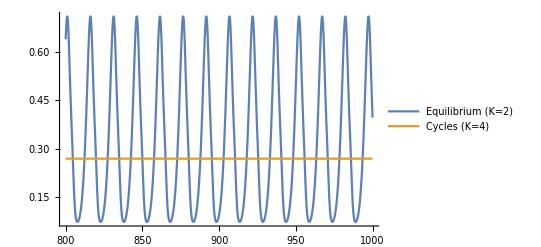
-Graphics-TimeTransmission Rate

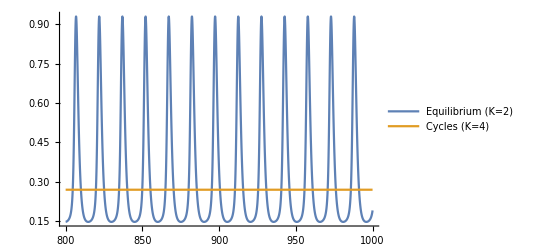
-Graphics-TimeMortality Rate

```mathematica
Labeled[Plot[{(B0 v S[t])/(1+v)/.soln/.params,(B0 v EndEq[[2,2]])/(1+v)/.params},{t,800,1000},PlotLegends->{"Equilibrium (K=2)","Cycles (K=4)"}],{"Time","Transmission Rate"},{Bottom,Left},RotateLabel->True,Alignment->Center]
Labeled[Plot[{(d+v)/((fs R[t])/(h+R[t]))/.soln/.params,(d+v)/((fs EndEq[[1,2]])/(h+EndEq[[1,2]]))/.params},{t,800,1000},PlotRange->All,PlotLegends->{"Equilibrium (K=2)","Cycles (K=4)"}],{"Time","Mortality Rate"},{Bottom,Left},RotateLabel->True,Alignment->Center]
```

NOTES:
How close is virulence to virulence needed to stabilize?
Is singular virulence ESS/CSS?

What about stage structure?
What about resource-dependent development?
Resource-dependent transmission?

### Parasite transmission is resource-dependent

```mathematica
(* The model *)
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q + Qm);
dS=(es fs R)/(h+R) (S+Q + Qm)-d S-B[R,v] S Q -B[R,vm] S Qm;
dQ=B[R,v] S Q-(d+v) Q;
dQm=B[R,vm]S Qm-(d+vm) Qm;

(* Stability analysis *)
(* Calculate the Jacobian *)
J=Simplify[{{D[dR,R],D[dR,S],D[dR,Q], D[dR,Qm]},{D[dS,R],D[dS,S],D[dS,Q], D[dS,Qm]},
{D[dQ,R],D[dQ,S],D[dQ,Q], D[dR,Qm]},
{D[dQm,R],D[dQm,S],D[dQm,Q], D[dQm,Qm]}}]
(* Evaluate the Jacobian at the equilibrium of interest (Qm=0) *)
MatrixForm[J/.{Qm->0}]
```

{{(-fs h K (Q+Qm+S)+(K-2 R) (h+R)^2 ρ)/(K (h+R)^2),-(fs R)/(h+R),-(fs R)/(h+R),-(fs R)/(h+R)},{-Q S B^(1,0)[R,v]+(es fs h (Q+Qm+S)-Qm (h+R)^2 S B^(1,0)[R,vm])/(h+R)^2,-d+(es fs R)/(h+R)-Q B[R,v]-Qm B[R,vm],(es fs R)/(h+R)-S B[R,v],(es fs R)/(h+R)-S B[R,vm]},{Q S B^(1,0)[R,v],Q B[R,v],-d-v+S B[R,v],-(fs R)/(h+R)},{Qm S B^(1,0)[R,vm],Qm B[R,vm],0,-d-vm+S B[R,vm]}}

((-fs h K (Q+S)+(K-2 R) (h+R)^2 ρ)/(K (h+R)^2) | -(fs R)/(h+R) | -(fs R)/(h+R) | -(fs R)/(h+R)
(es fs h (Q+S))/(h+R)^2-Q S B^(1,0)[R,v] | -d+(es fs R)/(h+R)-Q B[R,v] | (es fs R)/(h+R)-S B[R,v] | (es fs R)/(h+R)-S B[R,vm]
Q S B^(1,0)[R,v] | Q B[R,v] | -d-v+S B[R,v] | -(fs R)/(h+R)
0 | 0 | 0 | -d-vm+S B[R,vm])

If the system goes to a stable equilibrium, the invasion fitness of the mutant is given by r=β_0(R̂,v_m)Ŝ-(v_m+d), where Ŝ is the equilibrium abundance of susceptibles and R̂ is the equilibrium abundance of resources, as these are determined by the interaction among host, resources, and the resident strain.

#### Finding the singular strategy when the resident dynamics go to a stable equilibrium

If the resident dynamics approach the stable equilibrium, we can calculate the singular strategy analytically. This will be a useful comparison point for situations where the dynamics are not stable.

```mathematica
(* The S equilibrium (in terms of R̂) *)
Seq=Solve[dQ==0,S]
```

{{S→(d+v)/B[R,v]}}

Writing the invasion fitness, r, in terms of this equilibrium. Plugging in the expression for Ŝ (which depends on R̂), r=((v-v_m)(v v_m-d))/(v (1+v_m))1/(f(R̂))

```mathematica
r=-d-vm+S B[R,vm]
r/.Seq[[1]]//Simplify
```

-d-vm+S B[R,vm]

-d-vm+((d+v) B[R,vm])/B[R,v]

To find the singular strategy, we need to find the root of (∂r)/(∂v_m)|_(v_m=v) .

```mathematica
(D[r/.Seq[[1]],vm]/.vm->v)//Simplify
```

-1+((d+v) B^(0,1)[R,v])/B[R,v]

To determine whether this is an ESS, we need to look at whether the derivative (∂^2 r)/(∂v_m^2)|_(v_m=v)≤ 0.

```mathematica
D[r/.Seq[[1]],{vm,2}]/.vm->v//Simplify
```

((d+v) B^(0,2)[R,v])/B[R,v]

To determine whether this is an CSS, we need to look at whether the derivative d/dv((∂r)/(∂v_m)|_(v_m=v))<0. Here we get something this much more complicated, because it depends on the sign of R̂'(v), as well as (∂β)/(∂R) and (∂^2 β)/(∂R∂v). If increasing resources increases the transmission rate (e.g., (∂β)/(∂R)>0), then

```mathematica
Expand[D[D[r/.Seq[[1]],vm]/.vm->v/.R->R[v],v]]
(* At the singular strategy *)
Solve[(D[r/.Seq[[1]],vm]/.vm->v)==0,Derivative[0,1][B][R,v]]
(* plugging that into the above *)
Simplify[Expand[D[D[r/.Seq[[1]],vm]/.vm->v/.R->R[v],v]]/.{Derivative[0,1][B][R[v],v]->B[R[v],v]/(d+v)}]
```

(B^(0,1)[R[v],v])/B[R[v],v]-(d (B^(0,1)[R[v],v])^2)/B[R[v],v]^2-(v (B^(0,1)[R[v],v])^2)/B[R[v],v]^2+(d B^(0,2)[R[v],v])/B[R[v],v]+(v B^(0,2)[R[v],v])/B[R[v],v]-(d R'[v] B^(0,1)[R[v],v] B^(1,0)[R[v],v])/B[R[v],v]^2-(v R'[v] B^(0,1)[R[v],v] B^(1,0)[R[v],v])/B[R[v],v]^2+(d R'[v] B^(1,1)[R[v],v])/B[R[v],v]+(v R'[v] B^(1,1)[R[v],v])/B[R[v],v]

{{B^(0,1)[R,v]→B[R,v]/(d+v)}}

((d+v) B^(0,2)[R[v],v]+R'[v] (-B^(1,0)[R[v],v]+(d+v) B^(1,1)[R[v],v]))/B[R[v],v]

Thus, if the dynamics go to an equilibrium, there is one singular strategy that is both evolutionarily and convergence stable. You can also see that there is no dependence of the singular strategy or the fitness gradient on host resources, indicating that changes in resources will have no effect when the system is stable. It seems plausible that resources will have no effect when the dynamics are unstable, though that remains to be seen. If that is the case, then you might expect the ESS to be fairly similar in both stable and unstable populations, so whether the parasite will stabilize the host dynamics or not depends on how close the resident-only system is to the stability boundary. If the system is just barely unstable in the absence of any parasitism, then the addition of parasites will tend to stabilize.